```mathematica
FNames=Table[StringJoin["boundary_",Table["0",8-{ToString[i]//StringLength}[[1]]]//StringJoin,ToString[i]],{i,0,6261,10}];
```

```mathematica
FNames//Length
```

44

#### Reading The Output

Here I create a list of names corresponding to the ones given in output by Jecco

```mathematica
Name=Table[StringJoin["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/NumericalBB3D_3p1/",FNames[[i]],".h5"],{i,FNames//Length}];
```

```mathematica
Name=Table[StringJoin["/home/giulio/University/PhD/JeccoNewTest/Jecco_G/examples/BB_AH_01_3p1/",FNames[[i]],".h5"],{i,FNames//Length}];
```

```mathematica
Name=Table[StringJoin["/home/giulio/University/PhD/JeccoGt2/examples/BBB_3p1/",FNames[[i]],".h5"],{i,FNames//Length}];
```

I import the files

#### Object 3

```mathematica
Timing[Obj3=Table[Import[Name[[i]],"Data"](*[[1]]*),{i,1,Name//Length}]];
```

How many files? That is, how many “screenshot” of the situation have we taken?

the entries of Obj correspond to [t,x,y,u]

```mathematica
-2,2,10,-8
```

```mathematica
Obj3[[2]]//Keys
```

{/data/10/fields/fy1,/data/10/fields/fx1,/data/10/fields/b13,/data/10/fields/a3,/data/10/fields/g3}

```mathematica
a3=Table[Obj3[[i,3]],{i,1,Obj3//Length}]
```

```mathematica
xValues={-5,-25/6,-10/3,-5/2,-5/3,-5/6,0,5/6,5/3,5/2,10/3,25/6};
yValues={-5,-235/48,-115/24,-75/16,-55/12,-215/48,-35/8,-205/48,-25/6,-65/16,-95/24,-185/48,-15/4,-175/48,-85/24,-55/16,-10/3,-155/48,-25/8,-145/48,-35/12,-45/16,-65/24,-125/48,-5/2,-115/48,-55/24,-35/16,-25/12,-95/48,-15/8,-85/48,-5/3,-25/16,-35/24,-65/48,-5/4,-55/48,-25/24,-15/16,-5/6,-35/48,-5/8,-25/48,-5/12,-5/16,-5/24,-5/48,0,5/48,5/24,5/16,5/12,25/48,5/8,35/48,5/6,15/16,25/24,55/48,5/4,65/48,35/24,25/16,5/3,85/48,15/8,95/48,25/12,35/16,55/24,115/48,5/2,125/48,65/24,45/16,35/12,145/48,25/8,155/48,10/3,55/16,85/24,175/48,15/4,185/48,95/24,65/16,25/6,205/48,35/8,215/48,55/12,75/16,115/24,235/48};
```

```mathematica
MyGrids=Table[{xValues[[j]],yValues[[i]],a3[[t,i,j,1]]},{t,1,Obj3//Length},{j,1,xValues//Length},{i,1,yValues//Length}];
```

```mathematica
MyGrids//Dimensions
```

{627,12,96,3}

```mathematica
GridToPlot=Table[MyGrids[[iii]]//Flatten[#,1]&,{iii,1,MyGrids//Length}];
```

```mathematica
MyGrids//Length
```

172

```mathematica
GridToPlot[[1]]
```

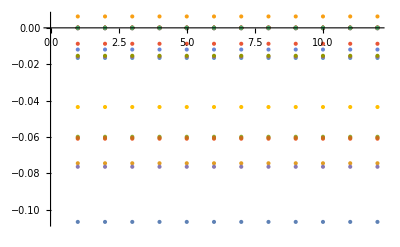

```mathematica
ListPlot[a3[[1;;300;;10,40,;;,1]]]
```

```mathematica
ListContourPlot[{GridToPlot[[1]],GridToPlot[[100]],GridToPlot[[200]],GridToPlot[[300]]},PlotLegends->Automatic,PlotLayout->"Row"]
```

-Graphics-

```mathematica
AnimationVideo[ListContourPlot[GridToPlot[[iii]](*,PlotLegends->Automatic*)],{iii,1,172,1},GeneratedAssetLocation->"/home/giulio/Videos/b.mp4"]
```

```mathematica
(*SBulk3=Table[Join[Obj3[[i,-1,20,20,;;-2]],Obj3[[i,2,20,20,;;-1]]]//Flatten,{i,1,FNames//Length}]*)
```

```mathematica
(*FxBulk3=Table[Join[Obj3[[i,5,20,20,;;-2]],Obj3[[i,4,20,20,;;-1]]]//Flatten,{i,1,FNames//Length}];*)
```

```mathematica
SBulk3SecondOne=Join[Obj3[[1,-2,;;,;;,;;-2]],Obj3[[1,2,;;,;;,;;-2]],Obj3[[1,12,;;,;;,;;-2]],Obj3[[1,-9,;;,;;,;;-2]],Obj3[[1,-5,;;,;;,;;-1]],3];
```

```mathematica
FxBulk3SecondOne=Join[Obj3[[1,6,;;,;;,;;-2]],Obj3[[1,5,;;,;;,;;-2]],Obj3[[1,-11,;;,;;,;;-2]],Obj3[[1,-13,;;,;;,;;-2]],Obj3[[1,-12,;;,;;,;;-1]],3];
FyBulk3SecondOne=Join[Obj3[[1,8,;;,;;,;;-2]],Obj3[[1,-6,;;,;;,;;-2]],Obj3[[1,7,;;,;;,;;-2]],Obj3[[1,11,;;,;;,;;-2]],Obj3[[1,14,;;,;;,;;-1]],3];
ABulk3SecondOne=Join[Obj3[[1,-2,;;,;;,;;-2]],Obj3[[1,3,;;,;;,;;-1]],3];
```

```mathematica
SBulk3SecondOne//Dimensions
(*FxBulk3SecondOne//Dimensions*)
```

{36,12,56}

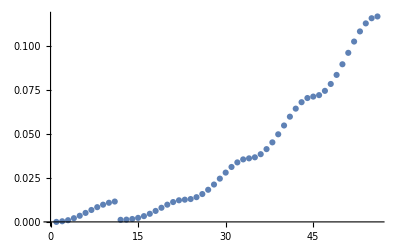

```mathematica
ListPlot[FyBulk3SecondOne[[10,1,;;]]]
```

```mathematica
FyBulk3SecondOne[[;;,1,;;]]
```

{{-2.35629×10^-34,1.70055×10^-21,2.49794×10^-21,1.60008×10^-21,2.59283×10^-21,-2.46276×10^-21,-6.67169×10^-21,-1.04402×10^-20,-1.36276×10^-20,-1.60826×10^-20,-1.76369×10^-20,-1.80808×10^-21,-1.01921×10^-18,-3.1515×10^-18,1.06079×10^-17,2.55228×10^-17,1.72858×10^-17,2.17428×10^-18,-3.35624×10^-19,-1.60293×10^-18,-2.46398×10^-18,-1.85262×10^-18,-1.57945×10^-18,-1.15595×10^-18,7.46421×10^-20,1.59477×10^-18,5.11255×10^-18,1.00132×10^-17,1.33289×10^-17,1.54239×10^-17,1.73453×10^-17,1.8904×10^-17,1.97446×10^-17,2.00133×10^-17,2.02793×10^-17,2.09136×10^-17,2.16245×10^-17,2.2446×10^-17,2.34599×10^-17,2.4546×10^-17,2.53449×10^-17,2.59215×10^-17,2.63425×10^-17,2.6645×10^-17,2.67523×10^-17,2.68548×10^-17,2.71163×10^-17,2.74061×10^-17,2.77552×10^-17,2.80707×10^-17,2.82463×10^-17,2.84362×10^-17,2.86557×10^-17,2.88283×10^-17,2.8937×10^-17,2.89765×10^-17},{-9.38892×10^-18,-0.000178603,-0.00048204,-0.00105503,-0.00174553,-0.00255467,-0.00338746,-0.00419146,-0.00489449,-0.00544193,-0.00578993,-0.000590815,-0.000646795,-0.00082429,-0.00114691,-0.00163854,-0.00230546,-0.00312109,-0.0040194,-0.00490027,-0.00564628,-0.00614689,-0.00632327,-0.00650215,-0.00703857,-0.00792732,-0.0091465,-0.0106434,-0.012324,-0.0140523,-0.0156607,-0.0169729,-0.0178327,-0.0181321,-0.0184341,-0.0193296,-0.0207843,-0.0227304,-0.025056,-0.0275999,-0.030156,-0.0324898,-0.0343664,-0.0355841,-0.036006,-0.0364305,-0.0376836,-0.0397018,-0.042371,-0.0455204,-0.0489217,-0.0522989,-0.0553512,-0.057786,-0.0593572,-0.0599002},{2.25197×10^-16,-0.00030935,-0.000834917,-0.00182736,-0.00302335,-0.00442481,-0.00586724,-0.0072598,-0.00847747,-0.00942563,-0.0100284,-0.00102331,-0.00112027,-0.00142769,-0.00198646,-0.00283793,-0.00399291,-0.00540532,-0.00696074,-0.00848576,-0.00977715,-0.0106436,-0.0109489,-0.0112585,-0.0121868,-0.0137247,-0.0158339,-0.0184228,-0.0213284,-0.0243149,-0.0270932,-0.029359,-0.030843,-0.0313597,-0.0318807,-0.0334257,-0.0359346,-0.0392889,-0.0432944,-0.0476721,-0.0520662,-0.0560742,-0.0592942,-0.0613819,-0.0621052,-0.0628326,-0.0649792,-0.0684336,-0.0729972,-0.0783737,-0.0841698,-0.0899137,-0.0950948,-0.0992205,-0.101879,-0.102797},{1.16299×10^-16,-0.000357206,-0.000964079,-0.00211006,-0.00349106,-0.00510933,-0.00677489,-0.00838286,-0.00978887,-0.0108837,-0.0115796,-0.00118161,-0.00129356,-0.00164852,-0.0022937,-0.00327678,-0.0046102,-0.00624063,-0.00803588,-0.00979575,-0.0112857,-0.0122853,-0.0126375,-0.0129946,-0.0140653,-0.0158387,-0.0182702,-0.0212534,-0.0245997,-0.0280372,-0.0312329,-0.0338374,-0.0355425,-0.0361361,-0.0367344,-0.0385083,-0.0413871,-0.0452327,-0.0498193,-0.0548245,-0.0598401,-0.0644069,-0.0680698,-0.0704418,-0.0712629,-0.0720884,-0.0745228,-0.0784343,-0.0835898,-0.0896448,-0.096147,-0.102562,-0.108321,-0.112887,-0.115819,-0.116829},{3.53558×10^-16,-0.00030935,-0.000834917,-0.00182736,-0.00302335,-0.00442481,-0.00586722,-0.00725974,-0.00847736,-0.00942546,-0.0100281,-0.00102329,-0.00112024,-0.00142764,-0.00198634,-0.00283762,-0.00399219,-0.00540377,-0.00695781,-0.00848096,-0.0097703,-0.0106352,-0.0109398,-0.0112488,-0.0121749,-0.0137086,-0.0158108,-0.0183889,-0.0212791,-0.0242461,-0.0270023,-0.0292472,-0.0307159,-0.0312271,-0.0317422,-0.0332691,-0.0357453,-0.0390495,-0.0429845,-0.0472706,-0.0515559,-0.0554483,-0.0585629,-0.0605759,-0.0612721,-0.0619715,-0.0640316,-0.0673336,-0.0716686,-0.0767308,-0.0821252,-0.0873957,-0.0920741,-0.0957399,-0.0980706,-0.0988693},{-1.79143×10^-16,-0.000178603,-0.00048204,-0.00105503,-0.00174553,-0.00255466,-0.00338743,-0.0041914,-0.00489438,-0.00544175,-0.0057897,-0.000590791,-0.000646765,-0.000824235,-0.00114678,-0.00163824,-0.00230474,-0.00311954,-0.00401648,-0.00489546,-0.00563942,-0.0061384,-0.00631416,-0.00649238,-0.00702664,-0.00791122,-0.0091234,-0.0106095,-0.0122748,-0.0139834,-0.0155697,-0.016861,-0.0177055,-0.0179993,-0.0182954,-0.0191727,-0.0205946,-0.0224903,-0.0247449,-0.0271964,-0.0296422,-0.0318583,-0.0336271,-0.034768,-0.035162,-0.0355577,-0.0367215,-0.0385813,-0.0410107,-0.0438257,-0.0467905,-0.0496388,-0.0521102,-0.0539941,-0.0551597,-0.0555521},{1.62368×10^-32,6.53721×10^-20,1.36897×10^-19,2.18772×10^-19,4.06834×10^-19,5.10852×10^-19,5.3074×10^-19,6.55985×10^-19,8.27023×10^-19,9.64635×10^-19,1.05333×10^-18,1.08147×10^-19,1.0257×10^-18,5.62176×10^-21,-1.82538×10^-17,-3.4328×10^-17,-4.50639×10^-17,-4.70743×10^-17,-4.20204×10^-17,-3.42592×10^-17,-2.74839×10^-17,-2.3309×10^-17,-2.1778×10^-17,-2.02678×10^-17,-1.60062×10^-17,-1.05081×10^-17,-4.19781×10^-18,3.45581×10^-18,1.21978×10^-17,1.92075×10^-17,2.51658×10^-17,2.97636×10^-17,3.26912×10^-17,3.36643×10^-17,3.45566×10^-17,3.70927×10^-17,4.09477×10^-17,4.54207×10^-17,4.97149×10^-17,5.35708×10^-17,5.73328×10^-17,6.00275×10^-17,6.19355×10^-17,6.30487×10^-17,6.34087×10^-17,6.37785×10^-17,6.47857×10^-17,6.61975×10^-17,6.7632×10^-17,6.88449×10^-17,6.95534×10^-17,6.92827×10^-17,6.83684×10^-17,6.70089×10^-17,6.58177×10^-17,6.53515×10^-17},{3.04626×10^-16,0.000178603,0.00048204,0.00105503,0.00174553,0.00255466,0.00338743,0.0041914,0.00489438,0.00544175,0.0057897,0.000590791,0.000646765,0.000824235,0.00114678,0.00163824,0.00230474,0.00311954,0.00401648,0.00489546,0.00563942,0.0061384,0.00631416,0.00649238,0.00702664,0.00791122,0.0091234,0.0106095,0.0122748,0.0139834,0.0155697,0.016861,0.0177055,0.0179993,0.0182954,0.0191727,0.0205946,0.0224903,0.0247449,0.0271964,0.0296422,0.0318583,0.0336271,0.034768,0.035162,0.0355577,0.0367215,0.0385813,0.0410107,0.0438257,0.0467905,0.0496388,0.0521102,0.0539941,0.0551597,0.0555521},{-3.11616×10^-16,0.00030935,0.000834917,0.00182736,0.00302335,0.00442481,0.00586722,0.00725974,0.00847736,0.00942546,0.0100281,0.00102329,0.00112024,0.00142764,0.00198634,0.00283762,0.00399219,0.00540377,0.00695781,0.00848096,0.0097703,0.0106352,0.0109398,0.0112488,0.0121749,0.0137086,0.0158108,0.0183889,0.0212791,0.0242461,0.0270023,0.0292472,0.0307159,0.0312271,0.0317422,0.0332691,0.0357453,0.0390495,0.0429845,0.0472706,0.0515559,0.0554483,0.0585629,0.0605759,0.0612721,0.0619715,0.0640316,0.0673336,0.0716686,0.0767308,0.0821252,0.0873957,0.0920741,0.0957399,0.0980706,0.0988693},{-1.16299×10^-16,0.000357206,0.000964079,0.00211006,0.00349106,0.00510933,0.00677489,0.00838286,0.00978887,0.0108837,0.0115796,0.00118161,0.00129356,0.00164852,0.0022937,0.00327678,0.0046102,0.00624063,0.00803588,0.00979575,0.0112857,0.0122853,0.0126375,0.0129946,0.0140653,0.0158387,0.0182702,0.0212534,0.0245997,0.0280372,0.0312329,0.0338374,0.0355425,0.0361361,0.0367344,0.0385083,0.0413871,0.0452327,0.0498193,0.0548245,0.0598401,0.0644069,0.0680698,0.0704418,0.0712629,0.0720884,0.0745228,0.0784343,0.0835898,0.0896448,0.096147,0.102562,0.108321,0.112887,0.115819,0.116829},{-2.25129×10^-16,0.00030935,0.000834917,0.00182736,0.00302335,0.00442481,0.00586724,0.0072598,0.00847747,0.00942563,0.0100284,0.00102331,0.00112027,0.00142769,0.00198646,0.00283793,0.00399291,0.00540532,0.00696074,0.00848576,0.00977715,0.0106436,0.0109489,0.0112585,0.0121868,0.0137247,0.0158339,0.0184228,0.0213284,0.0243149,0.0270932,0.029359,0.030843,0.0313597,0.0318807,0.0334257,0.0359346,0.0392889,0.0432944,0.0476721,0.0520662,0.0560742,0.0592942,0.0613819,0.0621052,0.0628326,0.0649792,0.0684336,0.0729972,0.0783737,0.0841698,0.0899137,0.0950948,0.0992205,0.101879,0.102797},{9.38892×10^-18,0.000178603,0.00048204,0.00105503,0.00174553,0.00255467,0.00338746,0.00419146,0.00489449,0.00544193,0.00578993,0.000590815,0.000646795,0.00082429,0.00114691,0.00163854,0.00230546,0.00312109,0.0040194,0.00490027,0.00564628,0.00614689,0.00632327,0.00650215,0.00703857,0.00792732,0.0091465,0.0106434,0.012324,0.0140523,0.0156607,0.0169729,0.0178327,0.0181321,0.0184341,0.0193296,0.0207843,0.0227304,0.025056,0.0275999,0.030156,0.0324898,0.0343664,0.0355841,0.036006,0.0364305,0.0376836,0.0397018,0.042371,0.0455204,0.0489217,0.0522989,0.0553512,0.057786,0.0593572,0.0599002}}

```mathematica
(*Transpose[FxBulk3SecondOne,{3,2,1}]*)
```

```mathematica
BBulk3Second=Table[Join[Obj3[[i,3,;;,;;,;;-2]],Obj3[[i,1,;;,;;,;;-1]],3],{i,1,FNames//Length}];
(*GBulk=Table[Join[Obj3[[i,1,1,20,;;]],Obj3[[i,6,1,20,;;]],Obj3[[i,4,1,20,;;]]]//Flatten,{i,1,FNames//Length}];*)
```

```mathematica
BBulk3SecondOne//Dimensions
```

{24,12,87}

```mathematica
BBulk3Second[[1,1,;;,50]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

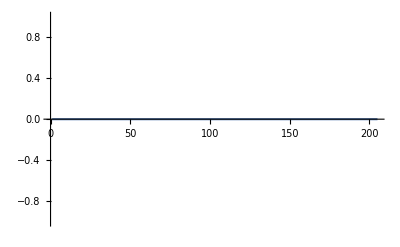

```mathematica
ListLinePlot[BBulk3Second[[1,1,2,;;]]]
```

```mathematica
ListPlot3D[SBulk3SecondOne[[1,;;,;;]],PlotRange->All]
```

-Graphics3D-

```mathematica
ListPlot3D[BBulk3Second[[90,1,;;,24;;]],PlotRange->All]
```

```mathematica
BBulk3[[1,-1]]
BBulk3[[-1,-1]]
```

-1.31544

-1.31559

```mathematica
Bbulk=Join[Obj3[[;;,3,1,1,;;]],Obj3[[;;,1,1,1,;;]],2];Gbulk=Join[Obj3[[;;,2,1,1,;;]],Obj3[[;;,4,1,1,;;]],2];
(*Gbulk=Join[Obj3[[;;,6,1,1,;;]],Obj3[[;;,5,1,1,;;]],Obj3[[;;,3,1,1,;;]],Obj3[[;;,-1,1,1,;;]],2];*)
```

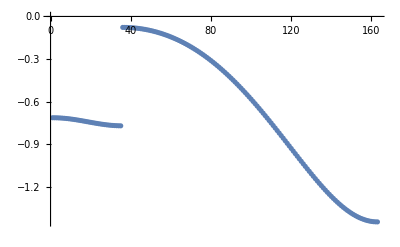

```mathematica
ListPlot[FxBulk3[[1]],PlotLegends->Automatic,PlotRange->All]
```

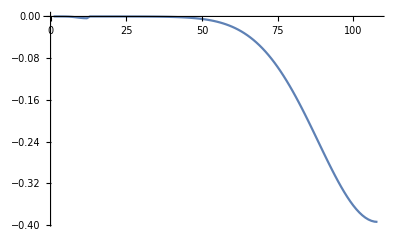

```mathematica
t=1;
ListPlot[Join[Obj3[[t,3,1,1,;;]],Obj3[[t,1,1,1,;;]]]//Flatten,Joined->True,PlotRange->All]
```

```mathematica
Obj3[[1,1,1,1,1]]
```

0.

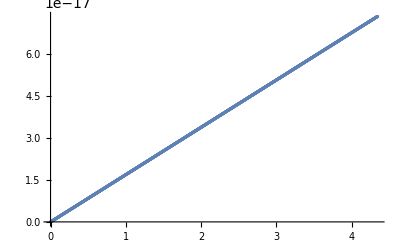

```mathematica
ListPlot[Table[{t 0.002,Obj3[[t,1,1,1,1]](*-Obj[[-1,3,1,1,1]]*)},{t,1,Obj3//Length}],PlotRange->All]
```

#### Obj

```mathematica
4,2,1,7
```

```mathematica
Obj[[1]]//Keys
```

{/data/0/fields/B c=3,/data/0/fields/B c=2,/data/0/fields/G c=3,/data/0/fields/B c=1,/data/0/fields/G c=2,/data/0/fields/G c=1,/data/0/fields/B c=4,/data/0/fields/G c=4}

```mathematica
ABulk=Table[Join[Obj[[i,-3,1,1,;;-2]],Obj[[i,4,1,1,;;-2]],Obj[[i,-4,1,1,;;-2]],Obj[[i,20,1,1,;;]]]//Flatten,{i,1,FNames//Length}];
SBulk=Table[Join[Obj[[i,-2,1,1,;;-2]],Obj[[i,2,1,1,;;-2]],Obj[[i,10,1,1,;;-2]],Obj[[i,-8,1,1,;;]]]//Flatten,{i,1,FNames//Length}];
(*BBulk=Table[Join[Obj[[i,4,1,1,;;-2]],Obj[[i,2,1,1,;;-2]],Obj[[i,1,1,1,;;-2]],Obj[[i,7,1,1,;;]]]//Flatten,{i,1,FNames//Length}];*)
```

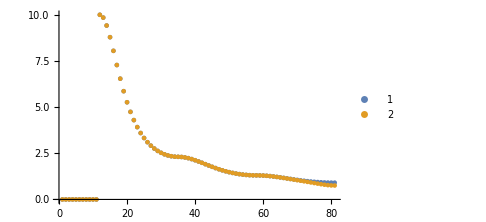

```mathematica
ListPlot[{SBulk[[1]],SBulk3[[1]]},PlotRange->All,PlotLegends->Automatic,ImageSize->Medium]
```

```mathematica
SBulk[[1]]
```

{0.,-7.76707×10^-43,8.86846×10^-42,-4.65005×10^-41,-9.79745×10^-41,-2.47831×10^-40,-5.64035×10^-40,-1.2603×10^-39,-2.8765×10^-39,-3.86754×10^-39,-4.32382×10^-39,10.,9.84714,9.41793,8.78749,8.04742,7.279,6.53989,5.86327,5.26346,4.74263,4.29632,3.91707,3.5966,3.32695,3.10097,2.91253,2.75649,2.62864,2.52556,2.44457,2.38359,2.34108,2.31599,2.30769,2.29945,2.27524,2.23648,2.18533,2.12443,2.05659,1.98457,1.91087,1.8376,1.7665,1.69887,1.63566,1.57751,1.52482,1.47781,1.43655,1.40103,1.37121,1.34698,1.32825,1.31495,1.30699,1.30435,1.30171,1.29392,1.28129,1.26433,1.24371,1.22015,1.19443,1.16733,1.13958,1.11182,1.08465,1.05853,1.03387,1.01097,0.990088,0.971396,0.955026,0.941071,0.929596,0.920639,0.914228,0.910376,0.909091}

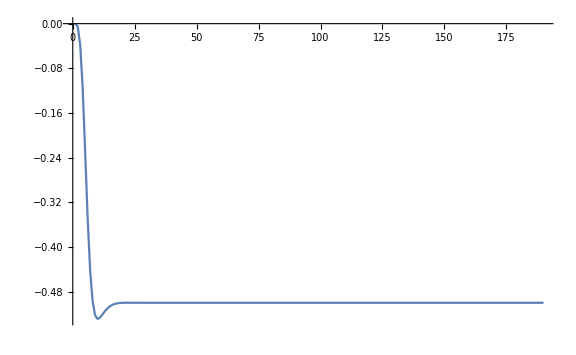

```mathematica
ListPlot[Obj[[;;,3,1,1,1]](*-Obj[[-1,3,1,1]]*),Joined->True,PlotRange->All,PlotLegends->Automatic,ImageSize->Large]
```

```mathematica
Obj[[-1,3,1,1,1]]
```

2.35203×10^-12

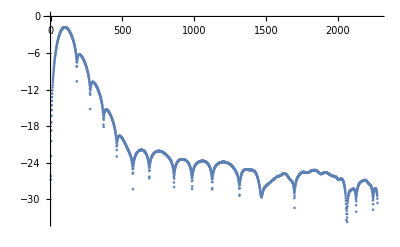

```mathematica
ListPlot[Log[Abs[Obj[[;;,3,1,1,1]]-Obj[[-1,3,1,1,1]]]],PlotRange->All]
```

Let’s visualize the initial data

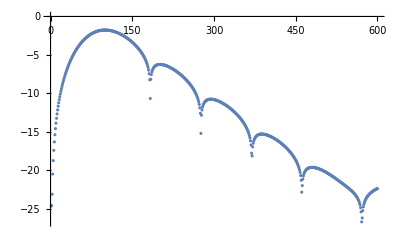

```mathematica
ListPlot[Log[Abs[Obj[[;;600,3,1,1,1]]-Obj[[600,5,1,1,1]]]],PlotRange->All]
```

```mathematica
ListContourPlot[Obj[[-1]][[4,;;,;;,1]](*,Contours->20*),ColorFunction->"SunsetColors",PlotLegends->Automatic]
```

-Graphics-

This Boundary5050 contains for each time a pair of values [t,phi(t) at the boundary]

```mathematica
Boundary5050=Table[{i 0.002,Obj[[i]][[3,1,1,1]]},{i,600(*Obj//Length*)}];
```

```mathematica
ToPlot=Table[{i,Log[Abs[Obj[[(*-1*)700]][[3,1,1,1]]-Obj[[i]][[3,1,1,1]]]]},{i,700(*Obj//Length*)}];
```

```mathematica
ToPlot[[2]]
```

{2,-0.287682}

```mathematica
Boundary5050[[1,2]]
```

0.

```mathematica
Boundary5050[[-1]]
```

{600,-1.76109×10^-10}

```mathematica
Boundary5050[[-1]]
```

{600,-1.76109×10^-10}

#### Exponential decay to the equilibrium value

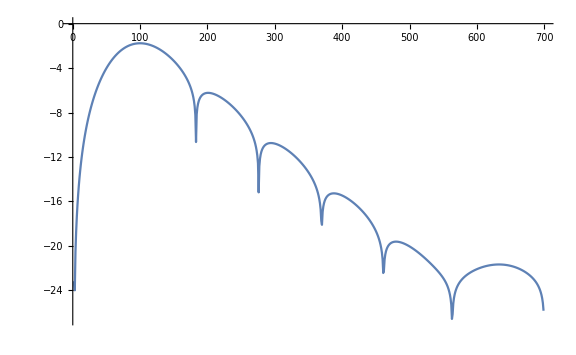

```mathematica
Show[ListPlot[ToPlot,Joined->True](*,ListPlot[Table[{(*0.04 *)i,(*Coeff*)(* 0.04 *)i}(*/.Coeff->-1.6*)5,{i,Obj//Length}],PlotStyle->Directive[PointSize[Small],Purple]]*),ImageSize->Large]
```

#### Quasi Normal Modes

```mathematica
Boundary5050[[-1,2]]
```

-1.76109×10^-10

```mathematica
Boundary5050//Length
```

600

```mathematica
FitRules1=FindFit[Boundary5050[[48;;]],Boundary5050[[-1,2]]+A1 E^(-ωi1 t)Cos[ωr1 t+δ1],{A1, ωi1,ωr1,δ1},t]
```

{A1→0.936301,ωi1→8.7347,ωr1→11.897,δ1→-2.81846}

```mathematica
FitRules2=FindFit[Boundary5050[[30;;]],Boundary5050[[-1,2]]+A1 E^(-ωi1 t)Cos[ωr1 t+δ1]+A2 E^(-ωi2 t)Cos[ωr2 t+δ2]/.FitRules1,{A2, ωi2,ωr2,δ2},t]
```

{A2→1.44452,ωi2→27.3171,ωr2→38.7984,δ2→-2.67968}

```mathematica
FitRules3=FindFit[Boundary5050,Boundary5050[[-1,2]]+A1 E^(-ωi1 t)Cos[ωr1 t+δ1]+A2 E^(-ωi2 t)Cos[ωr2 t+δ2]+A3 E^(-ωi3 t)Cos[ωr3 t+δ3]/.FitRules1/.FitRules2,{A3, ωi3,ωr3,δ3},t]
```

{A3→-0.0138179,ωi3→2.39203,ωr3→3.82919,δ3→1.41996}

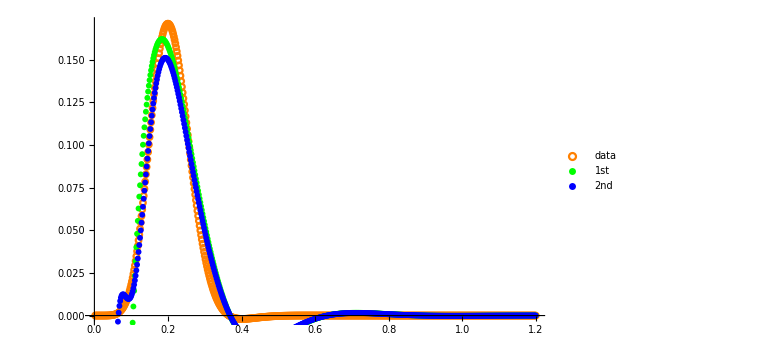

```mathematica
Show[ListPlot[Boundary5050(*,Joined->True*),PlotRange->All,PlotStyle->Orange,PlotMarkers->{Graphics[{Thickness[Small],Circle[{0,0}]}],0.015},PlotLegends->{"data"}],ListPlot[Table[{t,Boundary5050[[-1,2]]+(*A1*) E^(-ωi1 t)Cos[ωr1 t+δ1]/.FitRules1},{t,0,600 0.002,0.002}],PlotStyle->Green,PlotLegends->{"1st"}(*,PlotRange->All*)],ListPlot[Table[{t,Boundary5050[[-1,2]]+A1 E^(-ωi1 t)Cos[ωr1 t+δ1]+A2 E^(-ωi2 t)Cos[ωr2 t+δ2]/.FitRules1/.FitRules2},{t,0,600 0.002,0.002}],PlotStyle->Blue,PlotLegends->{"2nd"},PlotRange->All](*,Plot[Boundary5050[[-1,2]]+A1 E^(-ωi1 t)Cos[ωr1 t+δ1]+A2 E^(-ωi2 t)Cos[ωr2 t+δ2]+A3 E^(-ωi3 t)Cos[ωr3 t+δ3]/.FitRules1/.FitRules2/.FitRules3,{t,0,1},PlotStyle->Interpreter["Color"]["RGB 255 0 255"],PlotLegends->{"3rd"},PlotRange->All]*)(*,PlotRange->All*),ImageSize->Large]
```

```mathematica
E//N
```

2.71828

```mathematica
Name//Length
```

16

#### Visualizing the evolution

```mathematica
AnimationVideo[ListPlot3D[Obj[[a]][[4,;;,;;,1]](*,Contours->10*)(*,ColorFunction->"TemperatureMap"*)(*,PlotLegends->Automatic*),(*ContourStyle->None,*)PlotRange->{-1.2,1.2}],{a,1,Name//Length,1}];
```

## Benchmark

```mathematica
min=10^-7
```

1/10000000

```mathematica
NDSolve[{1/x^2 D[x^2 D[y[x],x],x]==-y[x]^3,y[min]==1,y'[min]==0},y,{x,min,5}]
```

{{y→InterpolatingFunction[…]}}

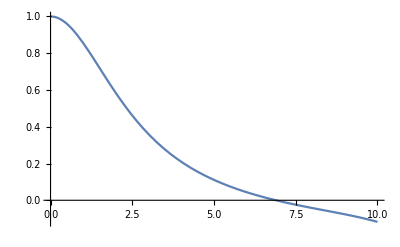

```mathematica
Plot[InterpolatingFunction[…][x],{x,min,10}]
```

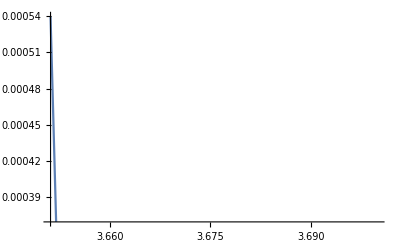

```mathematica
InterpolatingFunction
```

```mathematica
1
```

1

```mathematica
(InterpolatingFunction[…][Range[3,4,0.001]])
```

{0.158858+0. ⅈ,0.158573+0. ⅈ,0.158289+0. ⅈ,0.158005+0. ⅈ,0.157722+0. ⅈ,0.157438+0. ⅈ,0.157154+0. ⅈ,0.156871+0. ⅈ,0.156588+0. ⅈ,0.156304+0. ⅈ,0.156021+0. ⅈ,0.155738+0. ⅈ,0.155456+0. ⅈ,0.155173+0. ⅈ,0.15489+0. ⅈ,0.154608+0. ⅈ,0.154326+0. ⅈ,0.154044+0. ⅈ,0.153762+0. ⅈ,0.15348+0. ⅈ,0.153198+0. ⅈ,0.152916+0. ⅈ,0.152635+0. ⅈ,0.152353+0. ⅈ,0.152072+0. ⅈ,0.151791+0. ⅈ,0.15151+0. ⅈ,0.151229+0. ⅈ,0.150948+0. ⅈ,0.150667+0. ⅈ,0.150387+0. ⅈ,0.150106+0. ⅈ,0.149826+0. ⅈ,0.149546+0. ⅈ,0.149266+0. ⅈ,0.148986+0. ⅈ,0.148706+0. ⅈ,0.148427+0. ⅈ,0.148147+0. ⅈ,0.147868+0. ⅈ,0.147589+0. ⅈ,0.14731+0. ⅈ,0.147031+0. ⅈ,0.146752+0. ⅈ,0.146473+0. ⅈ,0.146194+0. ⅈ,0.145916+0. ⅈ,0.145637+0. ⅈ,0.145359+0. ⅈ,0.145081+0. ⅈ,0.144803+0. ⅈ,0.144525+0. ⅈ,0.144248+0. ⅈ,0.14397+0. ⅈ,0.143692+0. ⅈ,0.143415+0. ⅈ,0.143138+0. ⅈ,0.142861+0. ⅈ,0.142584+0. ⅈ,0.142307+0. ⅈ,0.14203+0. ⅈ,0.141754+0. ⅈ,0.141477+0. ⅈ,0.141201+0. ⅈ,0.140925+0. ⅈ,0.140649+0. ⅈ,0.140373+0. ⅈ,0.140097+0. ⅈ,0.139821+0. ⅈ,0.139546+0. ⅈ,0.13927+0. ⅈ,0.138995+0. ⅈ,0.13872+0. ⅈ,0.138445+0. ⅈ,0.13817+0. ⅈ,0.137895+0. ⅈ,0.13762+0. ⅈ,0.137346+0. ⅈ,0.137071+0. ⅈ,0.136797+0. ⅈ,0.136523+0. ⅈ,0.136249+0. ⅈ,0.135975+0. ⅈ,0.135701+0. ⅈ,0.135427+0. ⅈ,0.135154+0. ⅈ,0.134881+0. ⅈ,0.134607+0. ⅈ,0.134334+0. ⅈ,0.134061+0. ⅈ,0.133788+0. ⅈ,0.133515+0. ⅈ,0.133243+0. ⅈ,0.13297+0. ⅈ,0.132698+0. ⅈ,0.132426+0. ⅈ,0.132154+0. ⅈ,0.131882+0. ⅈ,0.13161+0. ⅈ,0.131338+0. ⅈ,0.131066+0. ⅈ,0.130795+0. ⅈ,0.130524+0. ⅈ,0.130252+0. ⅈ,0.129981+0. ⅈ,0.12971+0. ⅈ,0.129439+0. ⅈ,0.129169+0. ⅈ,0.128898+0. ⅈ,0.128628+0. ⅈ,0.128357+0. ⅈ,0.128087+0. ⅈ,0.127817+0. ⅈ,0.127547+0. ⅈ,0.127277+0. ⅈ,0.127008+0. ⅈ,0.126738+0. ⅈ,0.126469+0. ⅈ,0.126199+0. ⅈ,0.12593+0. ⅈ,0.125661+0. ⅈ,0.125392+0. ⅈ,0.125123+0. ⅈ,0.124855+0. ⅈ,0.124586+0. ⅈ,0.124318+0. ⅈ,0.124049+0. ⅈ,0.123781+0. ⅈ,0.123513+0. ⅈ,0.123245+0. ⅈ,0.122978+0. ⅈ,0.12271+0. ⅈ,0.122442+0. ⅈ,0.122175+0. ⅈ,0.121908+0. ⅈ,0.121641+0. ⅈ,0.121374+0. ⅈ,0.121107+0. ⅈ,0.12084+0. ⅈ,0.120573+0. ⅈ,0.120307+0. ⅈ,0.120041+0. ⅈ,0.119774+0. ⅈ,0.119508+0. ⅈ,0.119242+0. ⅈ,0.118976+0. ⅈ,0.118711+0. ⅈ,0.118445+0. ⅈ,0.11818+0. ⅈ,0.117914+0. ⅈ,0.117649+0. ⅈ,0.117384+0. ⅈ,0.117119+0. ⅈ,0.116854+0. ⅈ,0.116589+0. ⅈ,0.116325+0. ⅈ,0.11606+0. ⅈ,0.115796+0. ⅈ,0.115532+0. ⅈ,0.115268+0. ⅈ,0.115004+0. ⅈ,0.11474+0. ⅈ,0.114476+0. ⅈ,0.114213+0. ⅈ,0.113949+0. ⅈ,0.113686+0. ⅈ,0.113423+0. ⅈ,0.11316+0. ⅈ,0.112897+0. ⅈ,0.112634+0. ⅈ,0.112372+0. ⅈ,0.112109+0. ⅈ,0.111847+0. ⅈ,0.111584+0. ⅈ,0.111322+0. ⅈ,0.11106+0. ⅈ,0.110798+0. ⅈ,0.110537+0. ⅈ,0.110275+0. ⅈ,0.110013+0. ⅈ,0.109752+0. ⅈ,0.109491+0. ⅈ,0.10923+0. ⅈ,0.108969+0. ⅈ,0.108708+0. ⅈ,0.108447+0. ⅈ,0.108187+0. ⅈ,0.107926+0. ⅈ,0.107666+0. ⅈ,0.107405+0. ⅈ,0.107145+0. ⅈ,0.106885+0. ⅈ,0.106626+0. ⅈ,0.106366+0. ⅈ,0.106106+0. ⅈ,0.105847+0. ⅈ,0.105588+0. ⅈ,0.105328+0. ⅈ,0.105069+0. ⅈ,0.10481+0. ⅈ,0.104551+0. ⅈ,0.104293+0. ⅈ,0.104034+0. ⅈ,0.103776+0. ⅈ,0.103518+0. ⅈ,0.103259+0. ⅈ,0.103001+0. ⅈ,0.102743+0. ⅈ,0.102486+0. ⅈ,0.102228+0. ⅈ,0.10197+0. ⅈ,0.101713+0. ⅈ,0.101456+0. ⅈ,0.101199+0. ⅈ,0.100942+0. ⅈ,0.100685+0. ⅈ,0.100428+0. ⅈ,0.100171+0. ⅈ,0.0999147+0. ⅈ,0.0996583+0. ⅈ,0.0994021+0. ⅈ,0.0991459+0. ⅈ,0.0988899+0. ⅈ,0.0986341+0. ⅈ,0.0983783+0. ⅈ,0.0981227+0. ⅈ,0.0978672+0. ⅈ,0.0976118+0. ⅈ,0.0973566+0. ⅈ,0.0971015+0. ⅈ,0.0968465+0. ⅈ,0.0965917+0. ⅈ,0.0963369+0. ⅈ,0.0960823+0. ⅈ,0.0958279+0. ⅈ,0.0955735+0. ⅈ,0.0953193+0. ⅈ,0.0950652+0. ⅈ,0.0948113+0. ⅈ,0.0945574+0. ⅈ,0.0943037+0. ⅈ,0.0940502+0. ⅈ,0.0937967+0. ⅈ,0.0935434+0. ⅈ,0.0932902+0. ⅈ,0.0930371+0. ⅈ,0.0927842+0. ⅈ,0.0925314+0. ⅈ,0.0922787+0. ⅈ,0.0920261+0. ⅈ,0.0917737+0. ⅈ,0.0915214+0. ⅈ,0.0912692+0. ⅈ,0.0910172+0. ⅈ,0.0907653+0. ⅈ,0.0905135+0. ⅈ,0.0902618+0. ⅈ,0.0900103+0. ⅈ,0.0897589+0. ⅈ,0.0895076+0. ⅈ,0.0892564+0. ⅈ,0.0890054+0. ⅈ,0.0887545+0. ⅈ,0.0885037+0. ⅈ,0.0882531+0. ⅈ,0.0880026+0. ⅈ,0.0877522+0. ⅈ,0.0875019+0. ⅈ,0.0872518+0. ⅈ,0.0870018+0. ⅈ,0.0867519+0. ⅈ,0.0865022+0. ⅈ,0.0862525+0. ⅈ,0.086003+0. ⅈ,0.0857537+0. ⅈ,0.0855044+0. ⅈ,0.0852553+0. ⅈ,0.0850063+0. ⅈ,0.0847574+0. ⅈ,0.0845087+0. ⅈ,0.0842601+0. ⅈ,0.0840116+0. ⅈ,0.0837633+0. ⅈ,0.083515+0. ⅈ,0.0832669+0. ⅈ,0.083019+0. ⅈ,0.0827711+0. ⅈ,0.0825234+0. ⅈ,0.0822758+0. ⅈ,0.0820283+0. ⅈ,0.081781+0. ⅈ,0.0815338+0. ⅈ,0.0812867+0. ⅈ,0.0810397+0. ⅈ,0.0807929+0. ⅈ,0.0805462+0. ⅈ,0.0802996+0. ⅈ,0.0800532+0. ⅈ,0.0798069+0. ⅈ,0.0795607+0. ⅈ,0.0793146+0. ⅈ,0.0790687+0. ⅈ,0.0788228+0. ⅈ,0.0785771+0. ⅈ,0.0783316+0. ⅈ,0.0780861+0. ⅈ,0.0778408+0. ⅈ,0.0775957+0. ⅈ,0.0773506+0. ⅈ,0.0771057+0. ⅈ,0.0768609+0. ⅈ,0.0766162+0. ⅈ,0.0763716+0. ⅈ,0.0761272+0. ⅈ,0.0758829+0. ⅈ,0.0756388+0. ⅈ,0.0753947+0. ⅈ,0.0751508+0. ⅈ,0.074907+0. ⅈ,0.0746633+0. ⅈ,0.0744198+0. ⅈ,0.0741764+0. ⅈ,0.0739331+0. ⅈ,0.0736899+0. ⅈ,0.0734469+0. ⅈ,0.073204+0. ⅈ,0.0729612+0. ⅈ,0.0727186+0. ⅈ,0.072476+0. ⅈ,0.0722336+0. ⅈ,0.0719914+0. ⅈ,0.0717492+0. ⅈ,0.0715072+0. ⅈ,0.0712653+0. ⅈ,0.0710235+0. ⅈ,0.0707819+0. ⅈ,0.0705404+0. ⅈ,0.070299+0. ⅈ,0.0700577+0. ⅈ,0.0698166+0. ⅈ,0.0695755+0. ⅈ,0.0693347+0. ⅈ,0.0690939+0. ⅈ,0.0688533+0. ⅈ,0.0686127+0. ⅈ,0.0683724+0. ⅈ,0.0681321+0. ⅈ,0.067892+0. ⅈ,0.067652+0. ⅈ,0.0674121+0. ⅈ,0.0671723+0. ⅈ,0.0669327+0. ⅈ,0.0666932+0. ⅈ,0.0664538+0. ⅈ,0.0662145+0. ⅈ,0.0659754+0. ⅈ,0.0657364+0. ⅈ,0.0654975+0. ⅈ,0.0652588+0. ⅈ,0.0650202+0. ⅈ,0.0647817+0. ⅈ,0.0645433+0. ⅈ,0.064305+0. ⅈ,0.0640669+0. ⅈ,0.0638289+0. ⅈ,0.063591+0. ⅈ,0.0633533+0. ⅈ,0.0631157+0. ⅈ,0.0628782+0. ⅈ,0.0626408+0. ⅈ,0.0624035+0. ⅈ,0.0621664+0. ⅈ,0.0619294+0. ⅈ,0.0616926+0. ⅈ,0.0614558+0. ⅈ,0.0612192+0. ⅈ,0.0609827+0. ⅈ,0.0607463+0. ⅈ,0.0605101+0. ⅈ,0.0602739+0. ⅈ,0.0600379+0. ⅈ,0.0598021+0. ⅈ,0.0595663+0. ⅈ,0.0593307+0. ⅈ,0.0590952+0. ⅈ,0.0588598+0. ⅈ,0.0586246+0. ⅈ,0.0583895+0. ⅈ,0.0581545+0. ⅈ,0.0579196+0. ⅈ,0.0576848+0. ⅈ,0.0574502+0. ⅈ,0.0572157+0. ⅈ,0.0569813+0. ⅈ,0.0567471+0. ⅈ,0.056513+0. ⅈ,0.056279+0. ⅈ,0.0560451+0. ⅈ,0.0558113+0. ⅈ,0.0555777+0. ⅈ,0.0553442+0. ⅈ,0.0551108+0. ⅈ,0.0548776+0. ⅈ,0.0546444+0. ⅈ,0.0544114+0. ⅈ,0.0541785+0. ⅈ,0.0539458+0. ⅈ,0.0537131+0. ⅈ,0.0534806+0. ⅈ,0.0532482+0. ⅈ,0.053016+0. ⅈ,0.0527838+0. ⅈ,0.0525518+0. ⅈ,0.0523199+0. ⅈ,0.0520882+0. ⅈ,0.0518565+0. ⅈ,0.051625+0. ⅈ,0.0513936+0. ⅈ,0.0511623+0. ⅈ,0.0509312+0. ⅈ,0.0507002+0. ⅈ,0.0504693+0. ⅈ,0.0502385+0. ⅈ,0.0500078+0. ⅈ,0.0497773+0. ⅈ,0.0495469+0. ⅈ,0.0493166+0. ⅈ,0.0490864+0. ⅈ,0.0488564+0. ⅈ,0.0486265+0. ⅈ,0.0483967+0. ⅈ,0.048167+0. ⅈ,0.0479375+0. ⅈ,0.0477081+0. ⅈ,0.0474788+0. ⅈ,0.0472496+0. ⅈ,0.0470205+0. ⅈ,0.0467916+0. ⅈ,0.0465628+0. ⅈ,0.0463341+0. ⅈ,0.0461056+0. ⅈ,0.0458771+0. ⅈ,0.0456488+0. ⅈ,0.0454206+0. ⅈ,0.0451926+0. ⅈ,0.0449646+0. ⅈ,0.0447368+0. ⅈ,0.0445091+0. ⅈ,0.0442815+0. ⅈ,0.0440541+0. ⅈ,0.0438267+0. ⅈ,0.0435995+0. ⅈ,0.0433725+0. ⅈ,0.0431455+0. ⅈ,0.0429186+0. ⅈ,0.0426919+0. ⅈ,0.0424653+0. ⅈ,0.0422389+0. ⅈ,0.0420125+0. ⅈ,0.0417863+0. ⅈ,0.0415602+0. ⅈ,0.0413342+0. ⅈ,0.0411083+0. ⅈ,0.0408826+0. ⅈ,0.040657+0. ⅈ,0.0404315+0. ⅈ,0.0402061+0. ⅈ,0.0399808+0. ⅈ,0.0397557+0. ⅈ,0.0395307+0. ⅈ,0.0393058+0. ⅈ,0.0390811+0. ⅈ,0.0388564+0. ⅈ,0.0386319+0. ⅈ,0.0384075+0. ⅈ,0.0381832+0. ⅈ,0.0379591+0. ⅈ,0.037735+0. ⅈ,0.0375111+0. ⅈ,0.0372873+0. ⅈ,0.0370636+0. ⅈ,0.0368401+0. ⅈ,0.0366167+0. ⅈ,0.0363934+0. ⅈ,0.0361702+0. ⅈ,0.0359471+0. ⅈ,0.0357242+0. ⅈ,0.0355013+0. ⅈ,0.0352786+0. ⅈ,0.0350561+0. ⅈ,0.0348336+0. ⅈ,0.0346113+0. ⅈ,0.0343891+0. ⅈ,0.034167+0. ⅈ,0.033945+0. ⅈ,0.0337231+0. ⅈ,0.0335014+0. ⅈ,0.0332798+0. ⅈ,0.0330583+0. ⅈ,0.0328369+0. ⅈ,0.0326157+0. ⅈ,0.0323945+0. ⅈ,0.0321735+0. ⅈ,0.0319526+0. ⅈ,0.0317319+0. ⅈ,0.0315112+0. ⅈ,0.0312907+0. ⅈ,0.0310703+0. ⅈ,0.03085+0. ⅈ,0.0306298+0. ⅈ,0.0304098+0. ⅈ,0.0301898+0. ⅈ,0.02997+0. ⅈ,0.0297504+0. ⅈ,0.0295308+0. ⅈ,0.0293113+0. ⅈ,0.029092+0. ⅈ,0.0288728+0. ⅈ,0.0286537+0. ⅈ,0.0284347+0. ⅈ,0.0282159+0. ⅈ,0.0279972+0. ⅈ,0.0277785+0. ⅈ,0.0275601+0. ⅈ,0.0273417+0. ⅈ,0.0271234+0. ⅈ,0.0269053+0. ⅈ,0.0266873+0. ⅈ,0.0264694+0. ⅈ,0.0262516+0. ⅈ,0.026034+0. ⅈ,0.0258164+0. ⅈ,0.025599+0. ⅈ,0.0253817+0. ⅈ,0.0251645+0. ⅈ,0.0249475+0. ⅈ,0.0247305+0. ⅈ,0.0245137+0. ⅈ,0.024297+0. ⅈ,0.0240804+0. ⅈ,0.0238639+0. ⅈ,0.0236476+0. ⅈ,0.0234314+0. ⅈ,0.0232152+0. ⅈ,0.0229993+0. ⅈ,0.0227834+0. ⅈ,0.0225676+0. ⅈ,0.022352+0. ⅈ,0.0221365+0. ⅈ,0.0219211+0. ⅈ,0.0217058+0. ⅈ,0.0214906+0. ⅈ,0.0212756+0. ⅈ,0.0210606+0. ⅈ,0.0208458+0. ⅈ,0.0206311+0. ⅈ,0.0204165+0. ⅈ,0.0202021+0. ⅈ,0.0199877+0. ⅈ,0.0197735+0. ⅈ,0.0195594+0. ⅈ,0.0193454+0. ⅈ,0.0191316+0. ⅈ,0.0189178+0. ⅈ,0.0187042+0. ⅈ,0.0184906+0. ⅈ,0.0182772+0. ⅈ,0.018064+0. ⅈ,0.0178508+0. ⅈ,0.0176377+0. ⅈ,0.0174248+0. ⅈ,0.017212+0. ⅈ,0.0169993+0. ⅈ,0.0167867+0. ⅈ,0.0165742+0. ⅈ,0.0163619+0. ⅈ,0.0161497+0. ⅈ,0.0159375+0. ⅈ,0.0157255+0. ⅈ,0.0155137+0. ⅈ,0.0153019+0. ⅈ,0.0150902+0. ⅈ,0.0148787+0. ⅈ,0.0146673+0. ⅈ,0.014456+0. ⅈ,0.0142448+0. ⅈ,0.0140337+0. ⅈ,0.0138228+0. ⅈ,0.0136119+0. ⅈ,0.0134012+0. ⅈ,0.0131906+0. ⅈ,0.0129801+0. ⅈ,0.0127698+0. ⅈ,0.0125595+0. ⅈ,0.0123494+0. ⅈ,0.0121393+0. ⅈ,0.0119294+0. ⅈ,0.0117196+0. ⅈ,0.0115099+0. ⅈ,0.0113004+0. ⅈ,0.0110909+0. ⅈ,0.0108816+0. ⅈ,0.0106724+0. ⅈ,0.0104633+0. ⅈ,0.0102543+0. ⅈ,0.0100454+0. ⅈ,0.00983664+0. ⅈ,0.00962799+0. ⅈ,0.00941946+0. ⅈ,0.00921104+0. ⅈ,0.00900274+0. ⅈ,0.00879455+0. ⅈ,0.00858648+0. ⅈ,0.00837852+0. ⅈ,0.00817068+0. ⅈ,0.00796295+0. ⅈ,0.00775533+0. ⅈ,0.00754783+0. ⅈ,0.00734045+0. ⅈ,0.00713317+0. ⅈ,0.00692601+0. ⅈ,0.00671897+0. ⅈ,0.00651203+0. ⅈ,0.00630522+0. ⅈ,0.00609851+0. ⅈ,0.00589192+0. ⅈ,0.00568544+0. ⅈ,0.00547908+0. ⅈ,0.00527283+0. ⅈ,0.00506669+0. ⅈ,0.00486067+0. ⅈ,0.00465476+0. ⅈ,0.00444896+0. ⅈ,0.00424327+0. ⅈ,0.0040377+0. ⅈ,0.00383224+0. ⅈ,0.0036269+0. ⅈ,0.00342168+0. ⅈ,0.00321657+0. ⅈ,0.00301156+0. ⅈ,0.00280666+0. ⅈ,0.00260188+0. ⅈ,0.00239721+0. ⅈ,0.00219265+0. ⅈ,0.0019882+0. ⅈ,0.00178387+0. ⅈ,0.00157964+0. ⅈ,0.00137553+0. ⅈ,0.00117153+0. ⅈ,0.000967647+0. ⅈ,0.000763871+0. ⅈ,0.000560207+0. ⅈ,0.000356655+1.08689×10^-15 ⅈ,0.000153214+2.46305×10^-12 ⅈ,-0.000050116+1.43338×10^-11 ⅈ,-0.000253334+3.76355×10^-11 ⅈ,-0.000456442+7.10515×10^-11 ⅈ,-0.000659438+1.13807×10^-10 ⅈ,-0.000862323+1.69549×10^-10 ⅈ,-0.0010651+2.50499×10^-10 ⅈ,-0.00126776+3.74978×10^-10 ⅈ,-0.00147031+5.5302×10^-10 ⅈ,-0.00167276+7.87991×10^-10 ⅈ,-0.00187509+1.0828×10^-9 ⅈ,-0.00207731+1.44611×10^-9 ⅈ,-0.00227942+1.89791×10^-9 ⅈ,-0.00248142+2.4615×10^-9 ⅈ,-0.00268331+3.15287×10^-9 ⅈ,-0.00288509+3.98448×10^-9 ⅈ,-0.00308676+4.96807×10^-9 ⅈ,-0.00328832+6.11743×10^-9 ⅈ,-0.00348977+7.45115×10^-9 ⅈ,-0.00369111+8.99211×10^-9 ⅈ,-0.00389234+1.07604×10^-8 ⅈ,-0.00409347+1.27727×10^-8 ⅈ,-0.00429448+1.50447×10^-8 ⅈ,-0.00449538+1.75928×10^-8 ⅈ,-0.00469617+2.04374×10^-8 ⅈ,-0.00489686+2.36027×10^-8 ⅈ,-0.00509743+2.71124×10^-8 ⅈ,-0.0052979+3.09864×10^-8 ⅈ,-0.00549826+3.52436×10^-8 ⅈ,-0.00569851+3.99032×10^-8 ⅈ,-0.00589865+4.49869×10^-8 ⅈ,-0.00609868+5.0521×10^-8 ⅈ,-0.0062986+5.6535×10^-8 ⅈ,-0.00649841+6.30556×10^-8 ⅈ,-0.00669812+7.01061×10^-8 ⅈ,-0.00689772+7.77079×10^-8 ⅈ,-0.00709721+8.58808×10^-8 ⅈ,-0.00729659+9.46446×10^-8 ⅈ,-0.00749586+1.0402×10^-7 ⅈ,-0.00769503+1.14028×10^-7 ⅈ,-0.00789408+1.24695×10^-7 ⅈ,-0.00809303+1.36049×10^-7 ⅈ,-0.00829187+1.48123×10^-7 ⅈ,-0.00849061+1.6095×10^-7 ⅈ,-0.00868924+1.7456×10^-7 ⅈ,-0.00888775+1.8898×10^-7 ⅈ,-0.00908617+2.04237×10^-7 ⅈ,-0.00928447+2.20353×10^-7 ⅈ,-0.00948267+2.37354×10^-7 ⅈ,-0.00968076+2.55263×10^-7 ⅈ,-0.00987874+2.74108×10^-7 ⅈ,-0.0100766+2.93915×10^-7 ⅈ,-0.0102744+3.14716×10^-7 ⅈ,-0.0104721+3.36545×10^-7 ⅈ,-0.0106696+3.59436×10^-7 ⅈ,-0.0108671+3.83424×10^-7 ⅈ,-0.0110644+4.08539×10^-7 ⅈ,-0.0112616+4.34809×10^-7 ⅈ,-0.0114588+4.62262×10^-7 ⅈ,-0.0116558+4.90926×10^-7 ⅈ,-0.0118527+5.20828×10^-7 ⅈ,-0.0120495+5.51999×10^-7 ⅈ,-0.0122462+5.84467×10^-7 ⅈ,-0.0124428+6.18266×10^-7 ⅈ,-0.0126393+6.53433×10^-7 ⅈ,-0.0128357+6.90003×10^-7 ⅈ,-0.013032+7.28014×10^-7 ⅈ,-0.0132282+7.67497×10^-7 ⅈ,-0.0134242+8.08486×10^-7 ⅈ,-0.0136202+8.5101×10^-7 ⅈ,-0.0138161+8.951×10^-7 ⅈ,-0.0140118+9.40787×10^-7 ⅈ,-0.0142075+9.88102×10^-7 ⅈ,-0.014403+1.03708×10^-6 ⅈ,-0.0145985+1.08775×10^-6 ⅈ,-0.0147938+1.14016×10^-6 ⅈ,-0.014989+1.19433×10^-6 ⅈ,-0.0151842+1.25031×10^-6 ⅈ,-0.0153792+1.30813×10^-6 ⅈ,-0.0155741+1.36782×10^-6 ⅈ,-0.0157689+1.42941×10^-6 ⅈ,-0.0159636+1.49295×10^-6 ⅈ,-0.0161582+1.55847×10^-6 ⅈ,-0.0163527+1.62601×10^-6 ⅈ,-0.0165471+1.6956×10^-6 ⅈ,-0.0167414+1.76729×10^-6 ⅈ,-0.0169356+1.8411×10^-6 ⅈ,-0.0171297+1.91709×10^-6 ⅈ,-0.0173237+1.99527×10^-6 ⅈ,-0.0175176+2.0757×10^-6 ⅈ,-0.0177113+2.15841×10^-6 ⅈ,-0.017905+2.24343×10^-6 ⅈ,-0.0180986+2.3308×10^-6 ⅈ,-0.018292+2.42056×10^-6 ⅈ,-0.0184854+2.51274×10^-6 ⅈ,-0.0186787+2.60738×10^-6 ⅈ,-0.0188718+2.70451×10^-6 ⅈ,-0.0190649+2.80419×10^-6 ⅈ,-0.0192578+2.90644×10^-6 ⅈ,-0.0194507+3.0113×10^-6 ⅈ,-0.0196434+3.11882×10^-6 ⅈ,-0.019836+3.22904×10^-6 ⅈ,-0.0200286+3.34199×10^-6 ⅈ,-0.020221+3.45772×10^-6 ⅈ,-0.0204133+3.57627×10^-6 ⅈ,-0.0206056+3.69767×10^-6 ⅈ,-0.0207977+3.82197×10^-6 ⅈ,-0.0209897+3.94921×10^-6 ⅈ,-0.0211816+4.07942×10^-6 ⅈ,-0.0213735+4.21264×10^-6 ⅈ,-0.0215652+4.34891×10^-6 ⅈ,-0.0217568+4.48828×10^-6 ⅈ,-0.0219483+4.63079×10^-6 ⅈ,-0.0221397+4.77646×10^-6 ⅈ,-0.022331+4.92535×10^-6 ⅈ,-0.0225223+5.0775×10^-6 ⅈ,-0.0227134+5.23295×10^-6 ⅈ,-0.0229044+5.39174×10^-6 ⅈ,-0.0230953+5.5539×10^-6 ⅈ,-0.0232861+5.7195×10^-6 ⅈ,-0.0234768+5.88855×10^-6 ⅈ,-0.0236674+6.06112×10^-6 ⅈ,-0.0238579+6.23723×10^-6 ⅈ,-0.0240483+6.41694×10^-6 ⅈ,-0.0242386+6.60027×10^-6 ⅈ,-0.0244288+6.78729×10^-6 ⅈ,-0.0246189+6.97802×10^-6 ⅈ,-0.0248089+7.17252×10^-6 ⅈ,-0.0249988+7.37081×10^-6 ⅈ,-0.0251886+7.57295×10^-6 ⅈ,-0.0253783+7.77899×10^-6 ⅈ,-0.0255679+7.98895×10^-6 ⅈ,-0.0257574+8.20289×10^-6 ⅈ,-0.0259468+8.42085×10^-6 ⅈ,-0.0261361+8.64287×10^-6 ⅈ,-0.0263253+8.869×10^-6 ⅈ,-0.0265144+9.09928×10^-6 ⅈ,-0.0267034+9.33376×10^-6 ⅈ,-0.0268923+9.57247×10^-6 ⅈ,-0.0270811+9.81547×10^-6 ⅈ,-0.0272698+0.0000100628 ⅈ,-0.0274584+0.0000103145 ⅈ,-0.0276469+0.0000105706 ⅈ,-0.0278353+0.0000108312 ⅈ,-0.0280236+0.0000110963 ⅈ,-0.0282118+0.0000113659 ⅈ,-0.0283999+0.0000116401 ⅈ,-0.0285879+0.000011919 ⅈ,-0.0287758+0.0000122026 ⅈ,-0.0289636+0.0000124908 ⅈ,-0.0291513+0.0000127839 ⅈ,-0.0293389+0.0000130818 ⅈ,-0.0295264+0.0000133845 ⅈ,-0.0297138+0.0000136922 ⅈ,-0.0299011+0.0000140048 ⅈ,-0.0300883+0.0000143224 ⅈ,-0.0302755+0.0000146451 ⅈ,-0.0304625+0.0000149729 ⅈ,-0.0306494+0.0000153058 ⅈ,-0.0308362+0.0000156439 ⅈ,-0.0310229+0.0000159873 ⅈ,-0.0312096+0.0000163359 ⅈ,-0.0313961+0.0000166898 ⅈ,-0.0315825+0.0000170492 ⅈ,-0.0317688+0.0000174139 ⅈ,-0.0319551+0.0000177841 ⅈ,-0.0321412+0.0000181599 ⅈ,-0.0323273+0.0000185411 ⅈ,-0.0325132+0.000018928 ⅈ,-0.032699+0.0000193206 ⅈ,-0.0328848+0.0000197189 ⅈ,-0.0330704+0.0000201229 ⅈ,-0.033256+0.0000205327 ⅈ,-0.0334415+0.0000209483 ⅈ,-0.0336268+0.0000213699 ⅈ,-0.0338121+0.0000217974 ⅈ,-0.0339972+0.0000222309 ⅈ,-0.0341823+0.0000226704 ⅈ,-0.0343673+0.0000231161 ⅈ,-0.0345522+0.0000235678 ⅈ,-0.0347369+0.0000240258 ⅈ,-0.0349216+0.00002449 ⅈ,-0.0351062+0.0000249604 ⅈ,-0.0352907+0.0000254373 ⅈ,-0.0354751+0.0000259205 ⅈ,-0.0356594+0.0000264101 ⅈ,-0.0358436+0.0000269062 ⅈ,-0.0360277+0.0000274088 ⅈ,-0.0362117+0.000027918 ⅈ,-0.0363956+0.0000284339 ⅈ,-0.0365795+0.0000289564 ⅈ,-0.0367632+0.0000294856 ⅈ,-0.0369468+0.0000300216 ⅈ,-0.0371303+0.0000305644 ⅈ,-0.0373138+0.0000311141 ⅈ,-0.0374971+0.0000316707 ⅈ,-0.0376804+0.0000322343 ⅈ,-0.0378635+0.0000328048 ⅈ,-0.0380466+0.0000333825 ⅈ,-0.0382295+0.0000339673 ⅈ,-0.0384124+0.0000345592 ⅈ,-0.0385952+0.0000351584 ⅈ,-0.0387778+0.0000357648 ⅈ,-0.0389604+0.0000363785 ⅈ,-0.0391429+0.0000369997 ⅈ,-0.0393253+0.0000376282 ⅈ,-0.0395076+0.0000382642 ⅈ,-0.0396898+0.0000389077 ⅈ,-0.0398719+0.0000395588 ⅈ,-0.0400539+0.0000402176 ⅈ,-0.0402358+0.000040884 ⅈ,-0.0404177+0.0000415581 ⅈ,-0.0405994+0.00004224 ⅈ,-0.040781+0.0000429298 ⅈ,-0.0409626+0.0000436274 ⅈ,-0.041144+0.0000443329 ⅈ,-0.0413254+0.0000450464 ⅈ,-0.0415067+0.000045768 ⅈ,-0.0416878+0.0000464976 ⅈ,-0.0418689+0.0000472354 ⅈ,-0.0420499+0.0000479814 ⅈ,-0.0422308+0.0000487355 ⅈ,-0.0424116+0.000049498 ⅈ,-0.0425923+0.0000502688 ⅈ,-0.0427729+0.000051048 ⅈ,-0.0429534+0.0000518357 ⅈ,-0.0431338+0.0000526318 ⅈ,-0.0433141+0.0000534365 ⅈ,-0.0434944+0.0000542497 ⅈ,-0.0436745+0.0000550717 ⅈ,-0.0438546+0.0000559023 ⅈ,-0.0440345+0.0000567417 ⅈ,-0.0442144+0.0000575898 ⅈ,-0.0443942+0.0000584469 ⅈ,-0.0445738+0.0000593128 ⅈ,-0.0447534+0.0000601877 ⅈ,-0.0449329+0.0000610717 ⅈ,-0.0451123+0.0000619647 ⅈ,-0.0452916+0.0000628668 ⅈ,-0.0454709+0.0000637781 ⅈ,-0.04565+0.0000646986 ⅈ,-0.045829+0.0000656284 ⅈ,-0.046008+0.0000665675 ⅈ,-0.0461868+0.000067516 ⅈ,-0.0463656+0.000068474 ⅈ,-0.0465442+0.0000694414 ⅈ,-0.0467228+0.0000704184 ⅈ,-0.0469013+0.000071405 ⅈ,-0.0470797+0.0000724013 ⅈ,-0.047258+0.0000734072 ⅈ,-0.0474362+0.0000744229 ⅈ,-0.0476143+0.0000754484 ⅈ,-0.0477923+0.0000764838 ⅈ,-0.0479703+0.000077529 ⅈ,-0.0481481+0.0000785843 ⅈ,-0.0483259+0.0000796495 ⅈ,-0.0485035+0.0000807249 ⅈ,-0.0486811+0.0000818103 ⅈ,-0.0488586+0.000082906 ⅈ,-0.049036+0.0000840119 ⅈ,-0.0492133+0.000085128 ⅈ,-0.0493905+0.0000862546 ⅈ,-0.0495676+0.0000873915 ⅈ,-0.0497446+0.0000885388 ⅈ,-0.0499216+0.0000896967 ⅈ,-0.0500984+0.0000908652 ⅈ,-0.0502752+0.0000920442 ⅈ,-0.0504518+0.0000932339 ⅈ,-0.0506284+0.0000944344 ⅈ,-0.0508049+0.0000956456 ⅈ,-0.0509813+0.0000968676 ⅈ,-0.0511576+0.0000981006 ⅈ,-0.0513338+0.0000993445 ⅈ,-0.0515099+0.000100599 ⅈ,-0.051686+0.000101865 ⅈ,-0.0518619+0.000103142 ⅈ,-0.0520378+0.00010443 ⅈ,-0.0522136+0.00010573 ⅈ,-0.0523892+0.000107041 ⅈ,-0.0525648+0.000108363 ⅈ,-0.0527403+0.000109696 ⅈ,-0.0529157+0.000111041 ⅈ,-0.0530911+0.000112397 ⅈ,-0.0532663+0.000113765 ⅈ,-0.0534414+0.000115144 ⅈ,-0.0536165+0.000116535 ⅈ,-0.0537914+0.000117938 ⅈ,-0.0539663+0.000119353 ⅈ,-0.0541411+0.000120779 ⅈ,-0.0543158+0.000122217 ⅈ,-0.0544904+0.000123667 ⅈ,-0.0546649+0.000125129 ⅈ,-0.0548394+0.000126604 ⅈ,-0.0550137+0.00012809 ⅈ,-0.055188+0.000129588 ⅈ,-0.0553621+0.000131099 ⅈ,-0.0555362+0.000132622 ⅈ,-0.0557102+0.000134157 ⅈ,-0.0558841+0.000135704 ⅈ,-0.0560579+0.000137264 ⅈ,-0.0562317+0.000138837 ⅈ,-0.0564053+0.000140422 ⅈ,-0.0565789+0.000142019 ⅈ,-0.0567523+0.00014363 ⅈ,-0.0569257+0.000145252 ⅈ,-0.057099+0.000146888 ⅈ,-0.0572722+0.000148537 ⅈ,-0.0574453+0.000150198 ⅈ,-0.0576183+0.000151872 ⅈ,-0.0577913+0.00015356 ⅈ,-0.0579641+0.00015526 ⅈ,-0.0581369+0.000156973 ⅈ,-0.0583095+0.0001587 ⅈ,-0.0584821+0.00016044 ⅈ,-0.0586546+0.000162193 ⅈ,-0.0588271+0.000163959 ⅈ,-0.0589994+0.000165739 ⅈ,-0.0591716+0.000167532 ⅈ,-0.0593438+0.000169338 ⅈ,-0.0595158+0.000171159 ⅈ,-0.0596878+0.000172992 ⅈ,-0.0598597+0.00017484 ⅈ,-0.0600315+0.000176701 ⅈ,-0.0602033+0.000178576 ⅈ,-0.0603749+0.000180464 ⅈ,-0.0605464+0.000182367 ⅈ,-0.0607179+0.000184284 ⅈ,-0.0608893+0.000186214 ⅈ,-0.0610606+0.000188159 ⅈ,-0.0612318+0.000190117 ⅈ,-0.0614029+0.00019209 ⅈ,-0.0615739+0.000194077 ⅈ,-0.0617449+0.000196079 ⅈ,-0.0619157+0.000198094 ⅈ,-0.0620865+0.000200124 ⅈ,-0.0622572+0.000202169 ⅈ,-0.0624278+0.000204228 ⅈ,-0.0625983+0.000206302 ⅈ,-0.0627687+0.00020839 ⅈ,-0.0629391+0.000210493 ⅈ,-0.0631093+0.00021261 ⅈ,-0.0632795+0.000214743 ⅈ,-0.0634496+0.00021689 ⅈ,-0.0636196+0.000219052 ⅈ,-0.0637895+0.000221229 ⅈ,-0.0639594+0.000223421 ⅈ,-0.0641291+0.000225629 ⅈ,-0.0642988+0.000227851 ⅈ}